```mathematica
Clear[x,c,L,f,g,t,M,n,a,b]
NoTerms:=10
c:=0.5
L:=Pi
f[x_]:=Piecewise[{{0,x≥0&&x<0.1},{Sin[4x],x≥0.1&&x≤Pi/4},{0,x>Pi/4&&x≤L}}]
g[x_]:=0
a[n_]:=(2/L)*Integrate[f[x]*Sin[n*Pi*x/L],{x,0,L}]
b[n_]:=(2/(n*Pi*c))*Integrate[g[x]*Sin[n*Pi*x/L],{x,0,L}]

u[x_,t_,M_]:=Sum[(a[n]*Cos[n*Pi*c*t/L]+b[n]*Sin[n*Pi*c*t/L])*Sin[n*Pi*x/L],{n,1,M}]

z[x_,t_]:=Evaluate[u[x,t,NoTerms]]
```

```mathematica
Manipulate[Plot[z[x,t],{x,0,L},PlotRange->{-1.5,1.5}],{t,0,10,.2}]
```

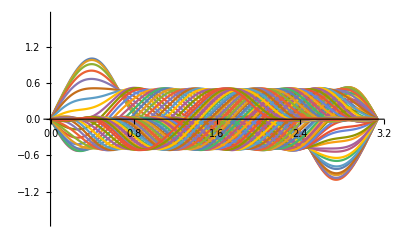

```mathematica
myTablePlot:=Table[z[x,t],{t,0,10,0.1}]
Plot[myTablePlot,{x,0,L},PlotRange->{-1.7,1.7}]
```

```mathematica
Manipulate[Plot3D[z[x-a,t],{x,0,L},{t,0,10},PlotRange->{-1.7,1.7},BoxRatios->{1, 1, 1}],{a,0,3}]
```

```mathematica
Simplify[Integrate[Cos[2x]*Sin[n*Pi*x/2],{x,0,2}],Assumptions->{n>0 && n ∈Integers}]
```

-(2 n π (-1+(-1)^n Cos[4]))/(-16+n^2 π^2)

```mathematica
f[x_]:=1/n*Sin[n*x]*x^2+2/n^2*Cos[n*x]*x-2/n^3*Sin[n*x]
```

```mathematica
f[x]
```

(2 x Cos[n x])/n^2-(2 Sin[n x])/n^3+(x^2 Sin[n x])/n

```mathematica
FullSimplify[D[f[x],x],Assumptions->{n>0 && n ∈Integers}]
```

x^2 Cos[n x]

```mathematica
Simplify[Integrate[x^2*Cos[n*x],{x,0,Pi}]*2/Pi,Assumptions->{n>0 && n ∈Integers}]
```

(4 (-1)^n)/n^2

```mathematica
Simplify[Integrate[x(1-x)*Sin[n*Pi*x],{x,0,1}]*2,,Assumptions->{n>0 && n ∈Integers}]
```

-(4 (-1+(-1)^n))/(n^3 π^3)

```mathematica
A[n_]:=Simplify[Integrate[x(5-x)*Sin[n*Pi*x/5],{x,0,5}],Assumptions->{n>0 && n ∈Integers}]*2/5
```

```mathematica
A[n]
```

-(100 (-1+(-1)^n))/(n^3 π^3)

```mathematica
Simplify[Integrate[x(3-x)*Cos[n*Pi*x/3],{x,0,3}],Assumptions->{n>0 && n ∈Integers}]*2/3
```

-(18 (1+(-1)^n))/(n^2 π^2)